```mathematica
filenames={
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost0_kHerb0.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost0_kHerb5.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost0_kHerb10.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost5_kHerb0.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost5_kHerb5.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost5_kHerb10.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost10_kHerb0.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost10_kHerb5.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost10_kHerb10.txt"
};
{rwcol,rrcol,wwcol}={RGBColor["#F2A35E"],RGBColor["#BF766F"],RGBColor["#7C92A6"]}
{RGBColor[0.9490196078431372, 0.6392156862745098, 0.3686274509803922],RGBColor[0.7490196078431373, 0.4627450980392157, 0.43529411764705883],RGBColor[0.48627450980392156, 0.5725490196078431, 0.6509803921568628]}
```

{RGBColor[0.9490196078431372, 0.6392156862745098, 0.3686274509803922],RGBColor[0.7490196078431373, 0.4627450980392157, 0.43529411764705883],RGBColor[0.48627450980392156, 0.5725490196078431, 0.6509803921568628]}

```mathematica
data=Table[Import[NotebookDirectory[]<>"../Data/"<>filenames⟦i⟧,"CSV"],{i,Length[filenames]}];
```

```mathematica
makeplot[datafile_]:={ListLogPlot[{datafile⟦2;;,5⟧,datafile⟦2;;,6⟧,datafile⟦2;;,7⟧}/10^4,Mesh->True,MeshStyle->PointSize[0.018],Joined->True,Frame->True,PlotRange->{Automatic,{10^-16,10^4}},PlotStyle->{Directive[Full,wwcol],Directive[Full,rwcol],Directive[Full,rrcol]},FrameStyle->Directive[Black,Thickness[0.003],FontSize->12],FrameLabel->{Style["Time(Years)",Black,16],Style["Plants / m^2",Black,16]},ImageSize->Large]}
```

```mathematica
Manipulate[makeplot[data⟦i⟧]⟦1⟧,{i,1,Length[filenames],1}]
```

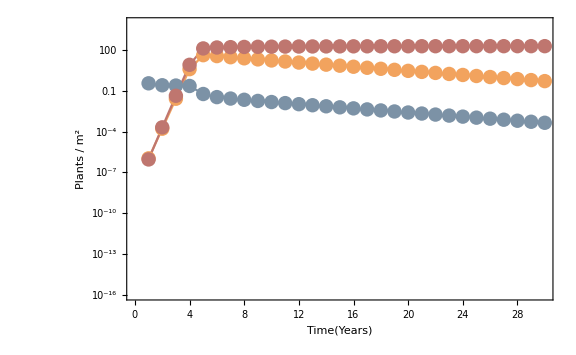
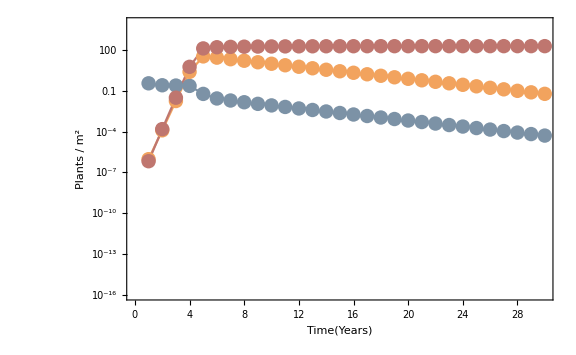
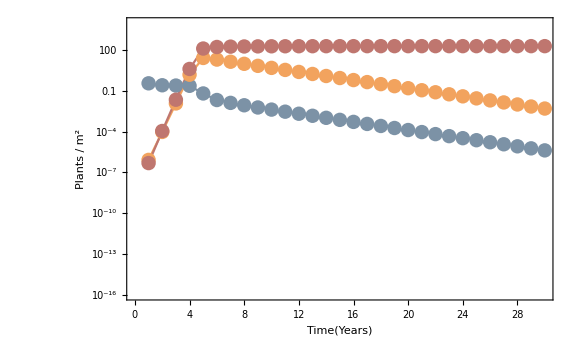
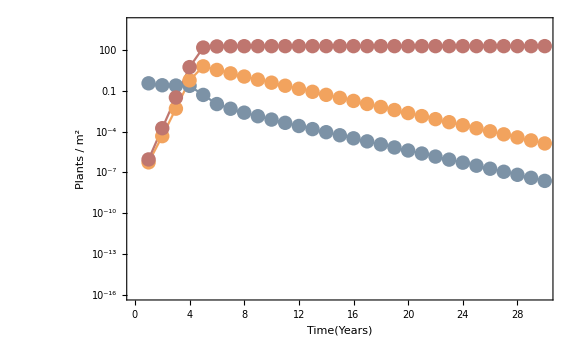
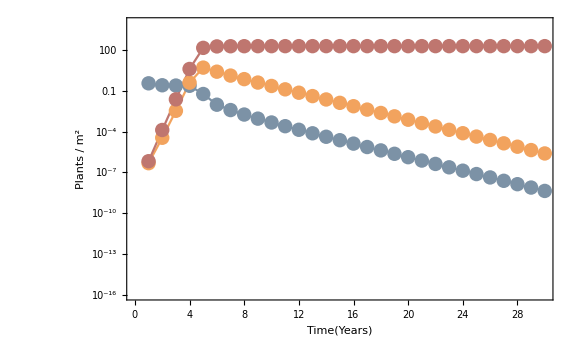
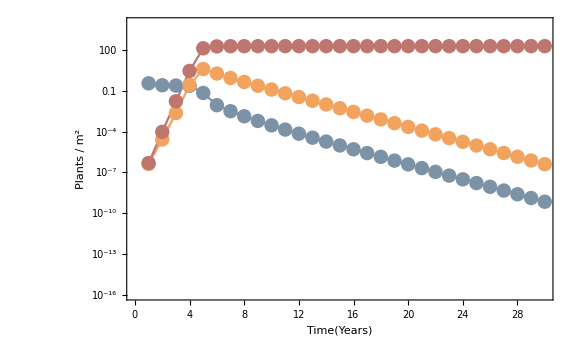
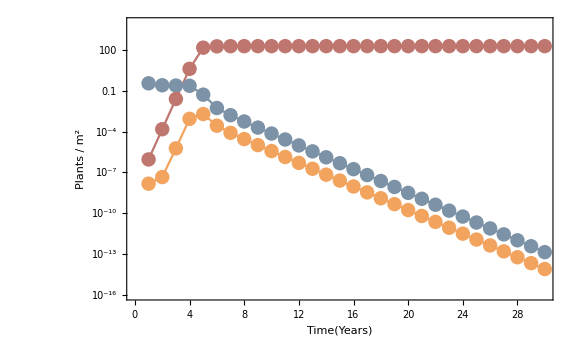
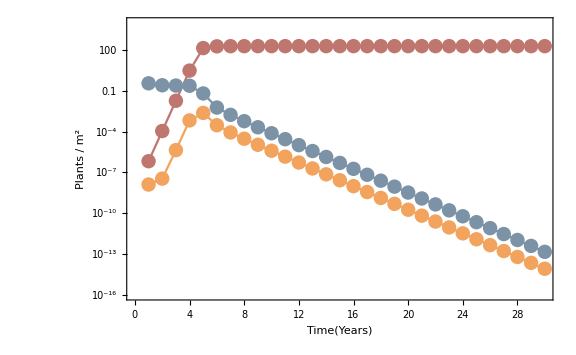

```mathematica
{{makeplot[data⟦3⟧]⟦1⟧,makeplot[data⟦6⟧]⟦1⟧,makeplot[data⟦9⟧]⟦1⟧},
{makeplot[data⟦2⟧]⟦1⟧,makeplot[data⟦5⟧]⟦1⟧,makeplot[data⟦8⟧]⟦1⟧},
{makeplot[data⟦1⟧]⟦1⟧,makeplot[data⟦4⟧]⟦1⟧,makeplot[data⟦7⟧]⟦1⟧}}
```